## Normal distribution

### The normal distribution function for a given argument “x” and the set of parameters: xargs -> {standard deviation, mean}

#### xargs=[σ , μ]

```mathematica
ClearAll["Global*`"]
```

```mathematica
fNormal[x_,xargs_]:=1/xargs[[1]]*1/(√(2π))Exp[-1/2*((x-xargs[[2]])/xargs[[1]])^2];
```

```mathematica
data[nsize_,left_,right_]:=Table[x,{x,left,right,(right-left)/nsize}];
mappedData[data_]:=Map[fNormal[#,{0.8,0}]&,data];
```

```mathematica
plotter[data_]:=ListPlot[Table[{data[[i]],mappedData[data][[i]]},{i,1,Length[data]}],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],Joined->True,PlotMarkers->{Automatic,Tiny}];
```

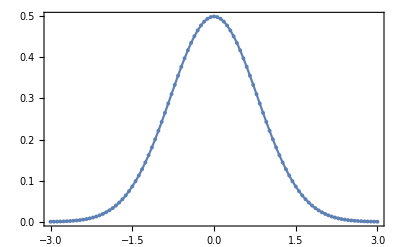

```mathematica
testdata=data[100,-3,3];
plotter[testdata]
```